# Лабораторная работа №11

Выполнила студентка ММФ БГУ
КМ, 1 к, 5 гр . Ковалевская В . С .
    17 ноября 2021

## Задание 1

```mathematica
{P1,P2,P3}=kmPoint/@{{-1,0},{5,3},{-2,2}}
```

{kmPoint[km,,{-1,0}],kmPoint[km,,{5,3}],kmPoint[km,,{-2,2}]}

```mathematica
kmPointShow[gp_List,opts___]:=Graphics[ReplaceAll[gp,P_kmPoint:>Tooltip[Point@P@"coord"]],Frame->True,GridLines->Automatic]
```

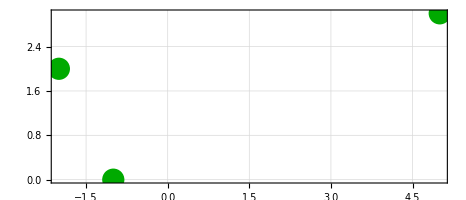

```mathematica
kmPointShow[{PointSize[0.04],Darker[Green],P1,P2,P3},Frame->True,GridLines->Automatic]
```

## Задание 2

```mathematica
(*объект точка на пл-ти*)
ClearAll[kmPoint];
kmPoint[coord:{_,_}]:=kmPoint[km,"",coord];
kmPoint[id_String,coord:{_,_}]:=kmPoint[km,id,coord];
kmPoint[{∅_,ρ_},"pol"]:=kmPoint[km,"",{ρ Cos[∅],ρ Sin[∅]}];
kmPoint[id_String,{∅_,ρ_},"pol"]:=kmPoint[km,id,{ρ Cos[∅],ρ Sin[∅]}];
kmPoint[km, id_String,___]["id"]:=If[id=="","Точка",id];
kmPoint[km,_String,coord_List,___]["coord"]:=coord;
NamedQ[kmPoint[km,id_String,___]]^:=id≠"";
kmGraphics2D[gp_List,opts___]:=Graphics[Point/@(#["coord"]&/@gp),opts];
kmPointShow[gp_List,opts___]:=Graphics[ReplaceAll[gp,P_kmPoint:>Tooltip[Point@P@"coord"]],Frame->True,GridLines->Automatic];
```

### 2.1

a) Создайте точку М, используя конструктор объекта «точка на 
плоскости»

```mathematica
kmPoint[id_String,coord:{_,_}]:=kmPoint[km,id,coord];
```

```mathematica
kmPoint["M",{(7 π)/4,1}]
```

kmPoint[km,M,{(7 π)/4,1}]

b) Получите декартовы координаты точки М

```mathematica
kmPoint["M",{(7 π)/4,1},"pol"]
```

kmPoint[km,M,{1/(√2),-1/(√2)}]

```mathematica
kmPoint["M",{(7 π)/4,1},"pol"]["coord"]
```

{1/(√2),-1/(√2)}

c) Получите имя точки.

```mathematica
kmPoint["M",{(7 π)/4,1},"pol"]["id"]
```

M

d) В графической области изобразите точку М зеленым цветом с 
использованием функции kmPointShow для отображения.

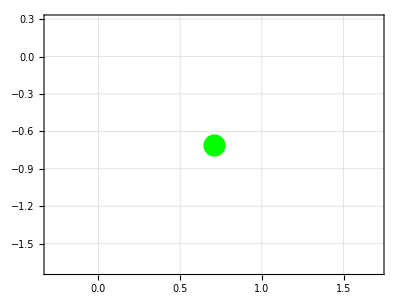

```mathematica
kmPointShow[{PointSize[0.04],Green,kmPoint["M",{(7 π)/4,1},"pol"]},Frame->True,GridLines->Automatic]
```

### 2.2

a) Используя конструкторы объекта «точка на плоскости», создайте точки  M и N, имеющие полярные координаты M(π/4, 2) и N(3π/4, 6)

```mathematica
M=kmPoint["M",{π/4,2},"pol"]
```

kmPoint[km,M,{√2,√2}]

```mathematica
Ν=kmPoint["Ν",{(3 π)/4,6},"pol"]
```

kmPoint[km,Ν,{-3 √2,3 √2}]

```mathematica
kmPoint["Ν",{(3 π)/4,6},"pol"]["coord"]
```

{-3 √2,3 √2}

b)Напишите функцию dist[P1_kmPoint,P2_kmPoint], которая 
вычисляет расстояние между двумя точками P1 и P2, заданными в 
системе «Аналитическая геометрия на плоскости»

```mathematica
a={-3 √2,3 √2};
b={√2,√2};
```

```mathematica
√(#.#)&[b-a]
```

2 √10

```mathematica
kmPoint[km,_String,coord_List,___]["coord"]:=coord;
```

```mathematica
dist[P1_kmPoint,P2_kmPoint]:=√(#.#)&[P2["coord"]-P1["coord"]]
```

```mathematica
dist[Ν,M]
```

2 √10

c) В графической области отобразите точку M красным цветом, точку N –  синим, отрезок, их соединяющий – серым; при этом точку, расположенную дальше от начала координат, отобразите большей по размеру, а также подпишите длину отрезка. Используйте функцию kmPointShow для отображения.

```mathematica
#["coord"]&/@{Ν,M}
```

{{-3 √2,3 √2},{√2,√2}}

```mathematica
Point/@(#["coord"]&/@{Ν,M})
```

{Point[{-3 √2,3 √2}],Point[{√2,√2}]}

```mathematica
(#["coord"]&/@{Ν,M})[[1]]
```

{-3 √2,3 √2}

```mathematica
Plus@@(#["coord"]&/@{Ν,M})
```

{-2 √2,4 √2}

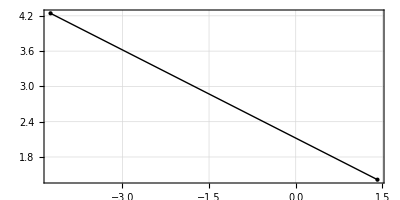

```mathematica
Graphics[{Point/@(#["coord"]&/@{Ν,M}), Line[#["coord"]&/@{Ν,M}]},Frame->True,GridLines->Automatic]
```

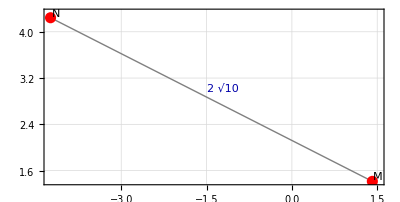

```mathematica
Graphics[{Gray,Line[#["coord"]&/@{Ν,M}],Darker[Blue],Text["2 √10",(Plus@@(#["coord"]&/@{Ν,M}))/2+0.2],
Black,MapThread[Text[#1,#2]&,{{"Ν","M"},#["coord"]&/@{Ν,M}+0.09}],PointSize[0.02],Red,Point/@(#["coord"]&/@{Ν,M})},Frame->True,GridLines->Automatic]
```

```mathematica
dist[M,kmPoint[{0,0}]]
```

2

```mathematica
dist[Ν,kmPoint[{0,0}]]
```

6

```mathematica
Graphics[{{Gray,Line[#["coord"]&/@{Ν,M}]},{Darker[Blue],Text["2 √10",(Plus@@(#["coord"]&/@{Ν,M}))/2+0.2]},
{Black,MapThread[Text[#1,#2]&,{{"Ν","M"},#["coord"]&/@{Ν,M}+0.12}]},{kmPointShow[{PointSize[0.04],Darker[Green],Ν,M}]}},Frame->True,GridLines->Automatic]
```

-Graphics-

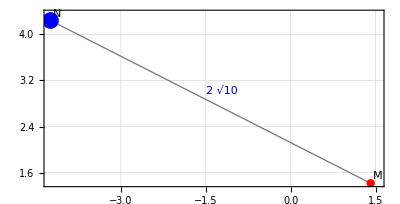

```mathematica
Graphics[{{Gray,Line[#["coord"]&/@{Ν,M}]},{Darker[Blue],Text["2 √10",(Plus@@(#["coord"]&/@{Ν,M}))/2+0.2]},
{Black,MapThread[Text[#1,#2]&,{{"Ν","M"},#["coord"]&/@{Ν,M}+0.12}]},{{PointSize[0.03],Blue,Point[Ν["coord"]]},{PointSize[0.015],Red,Point[M["coord"]]}}},Frame->True,GridLines->Automatic]
```

```mathematica
kmGraphShow[gp_kmPoint_List,opts___]:=Graphics[{{Gray,Line[#["coord"]&/@gp]},{{PointSize[0.03],Blue,Point[gp["coord"]]},{PointSize[0.015],Red,Point[gp["coord"]]}}},Frame->True,GridLines->Automatic]
```

```mathematica
Show[Graphics[{{kmPointShow[{PointSize[0.03],Blue,Point[Ν["coord"]]},{PointSize[0.015],Red,Point[M["coord"]]}]},{Gray,Line[#["coord"]&/@{Ν,M}]},{Darker[Blue],Text["2 √10",(Plus@@(#["coord"]&/@{Ν,M}))/2+0.2]},
{Black,MapThread[Text[#1,#2]&,{{"Ν","M"},#["coord"]&/@{Ν,M}+0.12}]}},Frame->True,GridLines->Automatic]]
```

-Graphics-

```mathematica
Graphics[{{kmPointShow[{PointSize[0.04],Darker[Green],P1,P2,P3},Frame->True,GridLines->Automatic]},{}
```

```mathematica
kmPointShow[{PointSize[0.04],Darker[Green],P1,P2,P3},Frame->True,GridLines->Automatic]
```

```mathematica
kmGraphShow[{M,N},Frame->True,GridLines->Automatic]
```

kmGraphShow[{kmPoint[km,M,{√2,√2}],N},Frame→True,GridLines→Automatic]

### 2.3

a) Точка С лежит на отрезке AB и делит его в отношении λ. Создайте 
конструктор, который строит объект «точка на плоскости» для 
представления точки С, если концы отрезка A и B заданы как объекты  «точка на плоскости».

```mathematica
kmPoint[{A_kmPoint,B_kmPoint,λ_},"otn"]:=kmPoint[km,(A["coord"]+λ B["coord"])/(1+λ)]
```

```mathematica
kmPoint[{Ν,M,2},"otn"]
```

kmPoint[km,{-(√2)/3,(5 √2)/3}]

```mathematica
kmPoint[id_String,otn:{A_kmPoint,B_kmPoint,λ_},"otn"]:=kmPoint[km,id,(A["coord"]+λ B["coord"])/(1+λ)](*создали конструктор для представления точки С, которая делит отрезок АВ в отношении λ*)
```

```mathematica
kmPoint["C",{Ν,M,2},"otn"]
```

kmPoint[km,C,{-(√2)/3,(5 √2)/3}]

```mathematica
Cc=kmPoint["C",{Ν,M,1/3},"otn"]
```

kmPoint[km,C,{-2 √2,5/(√2)}]

```mathematica
H=kmPoint["C",{Ν,M,2/3},"otn"]
```

kmPoint[km,C,{-(7 √2)/5,(11 √2)/5}]

```mathematica
K=kmPoint["C",{Ν,M,1},"otn"]
```

kmPoint[km,C,{-√2,2 √2}]

b) Отобразите в графической области следующие объекты: отрезок –  серым цветом, концы произвольного отрезка – красным; середину 
отрезка, а также точку, делящую отрезок в отношении 1/3 и точку, 
делящую отрезок в отношении 2/3 – синим цветом. Используйте 
функцию kmPointShow для отображения.

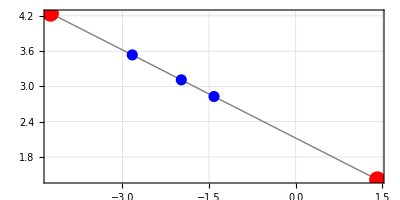

```mathematica
Graphics[{{Gray,Line[#["coord"]&/@{Ν,M}]},{{PointSize[0.03],Red,Point/@(#["coord"]&/@{Ν,M})}},{PointSize[0.02],Blue,Point[K["coord"]],Point[Cc["coord"]],Point[H["coord"]]}},Frame->True,GridLines->Automatic]
```

### 2.4

a) Треугольник ABC задан координатами своих вершин. Создайте три  объекта «точка на плоскости», каждый объект представляет одну вершину треугольника.

```mathematica
ClearAll[A,B,Cc];
```

```mathematica
A=kmPoint["A",{0,0}]
```

kmPoint[km,A,{0,0}]

```mathematica
B=kmPoint["B",{5,6}]
```

kmPoint[km,B,{5,6}]

```mathematica
Cc=kmPoint["C",{10,2}]
```

kmPoint[km,C,{10,2}]

b) Создайте конструктор объекта «точка на плоскости» kmPoint[triangle:{A_,B_,C_},”bisAcrossBC”] для представления точки D пересечения биссектрисы внутреннего угла A со стороной BC.

```mathematica
dist[A,B]
```

√61

```mathematica
Solve[dist[A,B]/dist[B,Cc]==(√(#.#)&[A["coord"]-k])/(√(#.#)&[k-Cc["coord"]]),k]//N//Values
```

{{5.02258},{31.5774}}

```mathematica
(Solve[dist[A,B]/dist[B,Cc]==(√(#.#)&[A["coord"]-k])/(√(#.#)&[k-Cc["coord"]]),k]//N//Values)//(First/@#)&
```

{5.02258,31.5774}

```mathematica
kmPoint[triangle:{A_,B_,C_},"bisAcrossBC"] :=kmPoint[km,(Solve[dist[A,B]/dist[B,Cc]==(√(#.#)&[A["coord"]-k])/(√(#.#)&[k-Cc["coord"]]),k]//N//Values)//(First/@#)&]
```

```mathematica
kmPoint[km,coord_List,___]["coord"] :=(Solve[dist[A,B]/dist[B,Cc]==(√(#.#)&[A["coord"]-k])/(√(#.#)&[k-Cc["coord"]]),k]//N//Values)//(First/@#)&
```

```mathematica
Dd=kmPoint[{A,B,Cc},"bisAcrossBC"]
```

kmPoint[km,{5.02258,31.5774}]

```mathematica
Dd["coord"]
```

{5.02258,31.5774}

c) В графической области отобразите произвольный треугольник. 
Отобразите точки пересечения биссектрис с противолежащими 
сторонами треугольника красным цветом. Отобразите биссектрисы 
зеленым цветом. Используйте функцию kmPointShow для отображения.

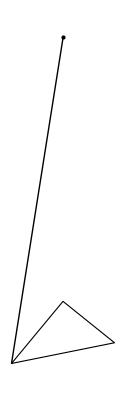

```mathematica
Graphics[{{FaceForm[White],EdgeForm[Directive[Thick,Black]],Polygon[{A["coord"],B["coord"],Cc["coord"]}]},
{Point[Dd["coord"]],Line[{A["coord"],Dd["coord"]}]}}]
```

### 2.5

a) Напишите пользовательскую функцию рolygonVertices, которая возвращает список вершин правильного n-угольника, вписанного в  окружность радиуса r, в виде геометрических объектов «точка на плоскости». 
Используйте метод построения вершин полигона в полярных координатах. Расположите полюс в точке О, являющейся центром n-угольника, а одну из вершин n-угольника – на полярной оси при нулевом угле ее поворота.

b) В графической области отобразите произвольный n-угольник, его вершины, объекты «точка на плоскости», красным цветом, а также описанную вокруг n-угольника окружность. 
Используйте функцию kmPointShow для отображения.

## Задание 3

### 3.1

kmVector[km , "id", {x, y}]

### 3.2

```mathematica
NamedQ[kmVector[km,id_String,___]]^:=id≠"";
```

### 3.3

```mathematica
kmVector[id_String,coord:{_,_}]:=kmVector[km,id,coord];
```

```mathematica
kmVector[coord_List]:=kmVector["",coord]
```

```mathematica
kmVector[{2,-1}]
```

kmVector[km,,{2,-1}]

```mathematica
kmVector[id_String,P0_kmPoint,P1_kmPoint]:=kmVector[id,P1["coord"]-P0["coord"]]
```

```mathematica
kmVector["v1",A,B]
```

kmVector[v1,A,B]

```mathematica
kmVector[km,id_String,coord:{_,_}]["id"]:=id;
```

```mathematica
kmVector[km,id_String,coord:{_,_}]["coord"]:=coord;
```

### 3.4

```mathematica
ClearAll[P1];
```

```mathematica
{P0,P1}=MapThread[kmPoint[#1,#2]&,{{"A","B"},{{3,4},{-2,3}}}]
```

{kmPoint[km,A,{3,4}],kmPoint[km,B,{-2,3}]}

```mathematica
P1@"coord"-P0@"coord"
```

{-5,-1}

```mathematica
kmVector[id_String,P0_kmPoint,P1_kmPoint]:=kmVector[id,P1@"coord"-P0@"coord"]
```

```mathematica
kmVector["CD",P0,P1]
```

kmVector[km,CD,{-5,-1}]

```mathematica
StringJoin[P0@"id",P1@"id"]
```

AB

```mathematica
And@@NamedQ/@{P0,P1}
```

True

```mathematica
kmVector[P0_kmPoint,P1_kmPoint]:=kmVector[If[And@@NamedQ/@{P0,P1},StringJoin[P0@"id",P1@"id"],""],P0,P1]
```

```mathematica
kmVector[P0,P1]
```

kmVector[km,AB,{-5,-1}]

```mathematica
√(#.#)&[P1["coord"]-P2["coord"]]
```

7

```mathematica
kmVector[km,id___String,coord_List,___]["length"]:=√(#.#)&[kmVector[id,coord]["coord"]]
```

```mathematica
kmVector[P0,P1]["length"]
```

√26

```mathematica
kmVector[id_String,
```

```mathematica
kmVector[km,_String,coord_List,___]["ort"]:=kmVector["",coord/(√(#.#)&coord)];
```